```mathematica
expAt=(1/(α-β))({{α E^(β t)-β E^(α t), E^(α t)-E^(β t)}, {Subscript[l, 1] E^(α t)-Subscript[l, 1] E^(β t), Subscript[l, 2] E^(α t)-Subscript[l, 2] E^(β t)+α E^(β t)-β E^(α t)}});
expAt//MatrixForm
```

((ⅇ^(t β) α-ⅇ^(t α) β)/(α-β) | (ⅇ^(t α)-ⅇ^(t β))/(α-β)
(ⅇ^(t α) l_1-ⅇ^(t β) l_1)/(α-β) | (ⅇ^(t β) α-ⅇ^(t α) β+ⅇ^(t α) l_2-ⅇ^(t β) l_2)/(α-β))

```mathematica
x0={{Subscript[x, 10]},{Subscript[x, 20]}};
expr=expAt. x0 ;
expr2=expr/.{α-> σ+ I ω,β-> σ- I ω};
(*expr2=Simplify[expr2];*)
term1=Collect[ComplexExpand[expr2[[1,1]]],Sin[t ω]];
term2=Collect[ComplexExpand[expr2[[2,1]]],Sin[t ω]];
term1=Collect[term1,E^(t σ)]
term2=Collect[term2,E^(t σ)]
ut=Subscript[l, 1] term1 +Subscript[l, 2] term2;
ut=Collect[Collect[ut,Cos[t ω]],Sin[t ω]]
```

ⅇ^(t σ) (Cos[t ω] x_10-(σ Sin[t ω] x_10)/ω+(Sin[t ω] x_20)/ω)

ⅇ^(t σ) ((Sin[t ω] l_1 x_10)/ω+Cos[t ω] x_20-(σ Sin[t ω] x_20)/ω+(Sin[t ω] l_2 x_20)/ω)

Cos[t ω] (ⅇ^(t σ) l_1 x_10+ⅇ^(t σ) l_2 x_20)+Sin[t ω] (-(ⅇ^(t σ) σ l_1 x_10)/ω+(ⅇ^(t σ) l_1 l_2 x_10)/ω+(ⅇ^(t σ) l_1 x_20)/ω-(ⅇ^(t σ) σ l_2 x_20)/ω+(ⅇ^(t σ) l_2^2 x_20)/ω)

```mathematica
A={{0,1},{0,0}};
B={{0},{1}};
Q=IdentityMatrix[2];
R={{1}};

P={{p1,p2},{p2,p3}};
sol=Solve[{Transpose[A].P+P.A-P.B.Inverse[R].Transpose[P.B]+Q==0,p1>0,p3>0},{p1,p2,p3},Reals];
sol=sol[[1]];
Pval=P/.sol;
Pval //N //MatrixForm
Eigenvalues[Pval]//N
```

(1.73205 | 1.
1. | 1.73205)

{2.73205,0.732051}

```mathematica
Clear[p1,p2,p3,r];
R={{r}};
P={{{Sqrt[1-2 Sqrt[r]],-Sqrt[r]},{-Sqrt[r],Sqrt[r (1-2 Sqrt[r])]}},{{Sqrt[1-2 Sqrt[r]],Sqrt[r]},{-Sqrt[r],Sqrt[r (1-2 Sqrt[r])]}},{{Sqrt[1+2 Sqrt[r]],-Sqrt[r]},{Sqrt[r],Sqrt[r (1+2 Sqrt[r])]}},{{Sqrt[1+2 Sqrt[r]],Sqrt[r]},{Sqrt[r],Sqrt[r (1+2 Sqrt[r])]}}};
Pval=P/.{r->1};
Rval=R/.{r->1};
Psol=Pval[[4]];
Psol//N//MatrixForm;
L=-Rval.Transpose[B].Psol;
L//N//MatrixForm;

lambda=Eigenvalues[A+B.L]//N;
sigma=Re[lambda[[1]]];
w=Im[lambda[[1]]];

Ac=A+B.L;
Ac//MatrixForm
Φ=MatrixExp[Ac t];
Φ=ComplexExpand[Φ];
Φ=Factor[Φ];
x0={{Subscript[x, 10]},{Subscript[x, 20]}};

tsol={t-> 0};
val=Simplify[L.Φ.x0]/.tsol;
val=val[[1]][[1]];
val//N
```

(0 | 1
-1 | -√3)

-1. x_10-1.73205 x_20

```mathematica
l1=L[[1,1]];
l2=L[[1,2]];
x10=x0[[1]];
x20=x0[[2]];
ut=(Exp[sigma t]/w)(x10(l1 w Cos[w t]+(l1 l2-sigma l1)Sin[w t])+x20((l1 -sigma l2+l2^2)Sin[w t]+l2 w Cos[w t]));
ut=Simplify[ut/.tsol];
ut[[1]]//N;

Simplify[MatrixExp[A+B.L]]//N//MatrixForm
MatrixExp[A].MatrixExp[B.L]//N//MatrixForm
```

(0.718407+0. ⅈ | 0.403312-2.77556×10^-17 ⅈ
-0.403312+2.77556×10^-17 ⅈ | 0.0198504-1.38778×10^-17 ⅈ)

(0.524795 | 0.176921
-0.475205 | 0.176921)

```mathematica
{vals,vecs}=Eigensystem[Ac];
Diag=DiagonalMatrix[vals];
P=Transpose[vecs];
PInv=Inverse[P];

(*Simplify[P.Diag.PInv]//N//MatrixForm*)
P//N//MatrixForm
Diag//N//MatrixForm
PInv//N//MatrixForm

Ac//N//MatrixForm

v1=Re[vecs[[1]]];
v2=Im[vecs[[1]]];
V=Transpose[{v1,v2}];
V//N//MatrixForm
(*
v1//N//MatrixForm
A.v1//N//MatrixForm
vals[[1]] v1//N//MatrixForm

Simplify[P.Diag.Inverse[P]]//N//MatrixForm
MatrixExp[Ac]//N
u.Exp[σ].Transpose[v]
Ac,u.σ.Transpose[v]
*)
```

(-0.866025-0.5 ⅈ | -0.866025+0.5 ⅈ
1. | 1.)

(-0.866025+0.5 ⅈ | 0.
0. | -0.866025-0.5 ⅈ)

(0.+1. ⅈ | 0.5+0.866025 ⅈ
0.-1. ⅈ | 0.5-0.866025 ⅈ)

(0. | 1.
-1. | -1.73205)

(-0.866025 | -0.5
1. | 0.)

```mathematica
A={{1,2},{-3,-4}};
B={{1,5},{-1,2}};
MatrixExp[A+B]//N//MatrixForm;
Caprox=MatrixPower[MatrixExp[A/n].MatrixExp[B/n],n];
Caprox/.{n->3} //N//MatrixForm;

MatApprox[X_]:=IdentityMatrix[Dimensions[X][[1]]]+X+X.X/2+X.X.X/6+X.X.X.X/24+X.X.X.X.X/120+X.X.X.X.X.X/720;
MatrixExp[A]//N//MatrixForm
MatApprox[A]//N//MatrixForm
```

(0.832968 | 0.465088
-0.697632 | -0.329753)

(0.793056 | 0.425
-0.6375 | -0.269444)

ⅇ^(-2 t) (-6+7 ⅇ^t)

2.04128

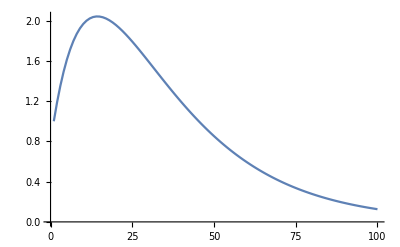

5

```mathematica
Linspace[start_,stop_,n_:100]:=Table[x,{x,start,stop,(stop-start)/(n-1)}];

A={{1,2},{-3,-4}};
x0={{1},{2}};
Φ=MatrixExp[A t];
xt=Φ .x0;
xt=Expand[Simplify[xt]];
xt[[1,1]]
x1vec=xt[[1,1]]/.{t->Linspace[0,4]}//N;
Max[x1vec]
ListLinePlot[x1vec]
Max[{Norm[A[[1]]],Norm[A[[2]]]}]
```